## Backcontinuation of spectral functions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/egull/Projects/Maxent/theory

Simple Gaussian

```mathematica
A[ω_]=1/Sqrt[2π]Exp[-ω^2/2];
```

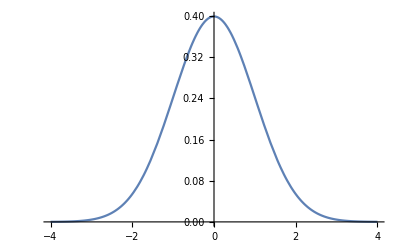

```mathematica
Plot[A[ω],{ω,-4,4}]
On[Assert];Assert[Integrate[A[ω],{ω,-Infinity, Infinity}]==1]
```

```mathematica
β=100.;
nmax=100;
```

```mathematica
iωntable=Table[I(2n+1)π/β,{n,0,nmax-1}];
```

```mathematica
Giωntable=Table[NIntegrate[A[ω]/(iωntable[[j]]-ω),{ω,-Infinity,Infinity}],{j,1,nmax}];
```

```mathematica
ωnReGiωntable=Table[{Im[iωntable[[j]]],Re[Giωntable[[j]]]},{j,1,nmax}];
ωnImGiωntable=Table[{Im[iωntable[[j]]],Im[Giωntable[[j]]]},{j,1,nmax}];
```

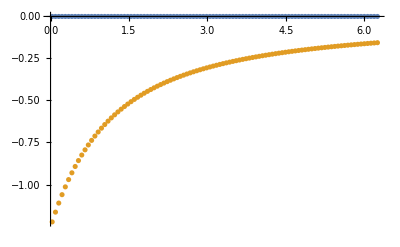

```mathematica
ListPlot[{ωnReGiωntable,ωnImGiωntable},PlotRange->All]
```

```mathematica
Export["GaussianHalfFilling.dat",ωnImGiωntable]
```

GaussianHalfFilling.dat

```mathematica
ωnImGiωntable[[1]]
```

{0.0314159,-1.22251}